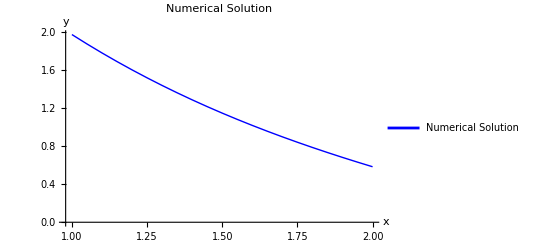

```mathematica
f[x_]:=-2 Exp[-2 x]

(*Коэффициенты краевых условий*)
a1=1;
b1=1;
gam1=0;
a2=0;
b2=1;
gam2=1;

(*Интервал интегрирования и параметры уравнения*)
stA=1;
stB=2;
p=0;  (*Коэффициент перед y'*)
q=-1; (*Коэффициент перед y*)
n=20;
h=(stB-stA)/n;

(*Коэффициенты разностной схемы*)
d=h^2*q-p*h-2;
e=1+p*h;

(*Вектор g для правой части*)
g=Table[h^2*f[stA+i*h],{i,0,n}];

(*Коэффициенты для краевых условий*)
X1=-b1/(a1*h-b1);
X2=b2/(a2*h+b2);
M1=gam1*h/(a1*h-b1);
M2=gam2*h/(a2*h-b2);

(*Инициализация списков Q и P*)
Q=Table[0,{n+1}];
P=Table[0,{n+1}];
Q[[1]]=X1;
P[[1]]=M1;

(*Вычисление Q и P для всех внутренних точек*)
For[i=1,i<=n,i++,Q[[i+1]]=-e/(Q[[i]]+d);
P[[i+1]]=(g[[i]]-P[[i]])/(Q[[i]]+d);];

(*Инициализация решения y*)
y=Table[0,{n+1}];

(*Учет правого краевого условия*)
y[[n+1]]=(M2+X2*P[[n+1]])/(1-Q[[n+1]]*X2);

(*Вычисление решения y для всех внутренних точек*)
For[i=n,i>=1,i--,y[[i]]=Q[[i]]*y[[i+1]]+P[[i]];];

(*Генерация массива x для графика*)
x=Table[stA+i*h,{i,0,n}];

(*Построение графиков численного решения*)
ListLinePlot[Transpose[{x,y}],PlotLabel->"Numerical Solution",PlotLegends->{"Numerical Solution"},AxesLabel->{"x","y"},PlotStyle->{Blue,Thick}]
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
deqn=y''[x]-y[x]==-2 Exp[-2 x];
sol=DSolve[deqn,y[x],x]
dsolution=D[y[x]/. sol[[1]],x]
bc1=(y[1]+dsolution/. x->1)==0
bc2=(dsolution/. x->2)==1
constants=Solve[{bc1,bc2},{C[1],C[2]}]
finalSolution=y[x]/. sol[[1]]/. constants[[1]]
finalSolution
```

{{y[x]→-2/3 ⅇ^(-2 x)+ⅇ^x C[1]+ⅇ^-x C[2]}}

(4 ⅇ^(-2 x))/3+ⅇ^x C[1]-ⅇ^-x C[2]

4/(3 ⅇ^2)+ⅇ C[1]-C[2]/ⅇ+y[1]==0

4/(3 ⅇ^4)+ⅇ^2 C[1]-C[2]/ⅇ^2==1

{{C[1]→-(4-4 ⅇ-3 ⅇ^4-3 ⅇ^3 y[1])/(3 ⅇ^4 (-1+ⅇ^2)),C[2]→-(4-4 ⅇ^3-3 ⅇ^4-3 ⅇ^5 y[1])/(3 ⅇ^2 (-1+ⅇ^2))}}

-2/3 ⅇ^(-2 x)-(ⅇ^(-4+x) (4-4 ⅇ-3 ⅇ^4-3 ⅇ^3 y[1]))/(3 (-1+ⅇ^2))-(ⅇ^(-2-x) (4-4 ⅇ^3-3 ⅇ^4-3 ⅇ^5 y[1]))/(3 (-1+ⅇ^2))

-2/3 ⅇ^(-2 x)-(ⅇ^(-4+x) (4-4 ⅇ-3 ⅇ^4-3 ⅇ^3 y[1]))/(3 (-1+ⅇ^2))-(ⅇ^(-2-x) (4-4 ⅇ^3-3 ⅇ^4-3 ⅇ^5 y[1]))/(3 (-1+ⅇ^2))

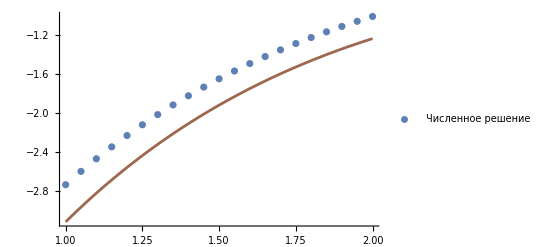

```mathematica
(*Параметры уравнения и краевые условия*)p=0;
q=-1;
f[x_]:=-2 Exp[-2 x];
n=20;
a=1;
b=2;
h=(b-a)/n;
Subscript[x,0]=a;
Subscript[x,n]=b;

(*Основное уравнение*)
mainEq=Table[Subscript[x,i]=Subscript[x,i-1]+h;
(Subscript[y,i-1]-2 Subscript[y,i]+Subscript[y,i+1])/h^2+p (Subscript[y,i+1]-Subscript[y,i])/h+q Subscript[y,i]==f[Subscript[x,i]],{i,1,n-1}];

(*Краевые условия*)
boundary={(Subscript[y,1]-Subscript[y,0])/h+Subscript[y,0]==0,(Subscript[y,n]-Subscript[y,n-1])/h==1};

(*Все уравнения*)
allEq=Join[mainEq,boundary];

(*Решение уравнений*)
sol=Solve[allEq,Table[Subscript[y,i],{i,0,n}]]//N;
val=Table[sol[[1,i,2]],{i,1,n+1}];
xs=Table[Subscript[x,i],{i,0,n}];
points=Transpose[{xs,val}];

(*Построение численного решения*)
gr1=ListPlot[points,PlotLegends->{"Численное решение"}];

(*Точное решение*)
realSolution=DSolve[{y''[x]-y[x]==-2 Exp[-2 x],y[1]+y'[1]==0,y'[2]==1},y[x],x];
gr2=Plot[Evaluate[y[x]/. realSolution],{x,1,2},ColorFunction->"DarkRainbow",PlotLegends->{"Точное решение"}];

(*Объединение графиков*)
Show[{gr1,gr2},PlotRange->All]
```